```mathematica
weightedLeastSquares[qq0_,id_,w_]:=Block[{rhovec,nu,s,r},
rhovec=Inverse[Transpose[qq0].w.qq0].Transpose[qq0] . w.id;
nu = Dimensions[w][[1]]-Length[rhovec];
r=(qq0.rhovec-id);
s=r.w.r;
Return[{rhovec,(Diagonal[Inverse[Transpose[qq0].w.qq0]])^(-1),r, s/nu}]];
```

```mathematica
points={{1,2},{3,6},{-1/2,-1/2}, {4,7},{5,10},{9,19},{2,4},{-6,-11},{21,40},{-7,-15}};
```

```mathematica
errvec=Table[RandomReal[],{i,1,10}];
```

```mathematica
coef=Transpose[{points[[;;,1]],Table[1,{i,1,10}]}]
```

{{1,1},{3,1},{-1/2,1},{4,1},{5,1},{9,1},{2,1},{-6,1},{21,1},{-7,1}}

```mathematica
results=weightedLeastSquares[coef,points[[;;,2]],DiagonalMatrix[errvec^(-2)]]
```

{{1.96012,-0.861201},{50529.3,415.233},{-0.901079,-0.980834,-1.34126,-0.020712,-1.06059,-2.2201,-0.940957,-1.62194,0.301368,0.417942},31.117}

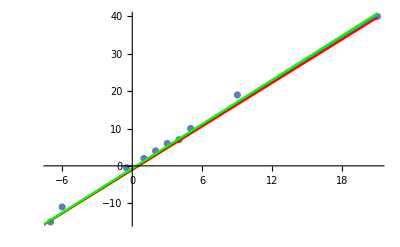

```mathematica
gpoints=ListPlot[points];
gline=Plot[x results[[1,1]]+ results[[1,2]], {x,-10,21}];
glinemin=Plot[x( results[[1,1]]-4results[[2,1]]^(-1/2))+ results[[1,2]]-4results[[2,2]]^(-1/2), {x,-10,21},PlotStyle->Red];
glinemax=Plot[x( results[[1,1]]+4results[[2,1]]^(-1/2))+ results[[1,2]]+4results[[2,2]]^(-1/2), {x,-10,21},PlotStyle->Green];
Show[gpoints,gline,glinemin,glinemax]
```

```mathematica
coef//Dimensions
```

{10,2}

```mathematica
DiagonalMatrix[errvec^(-2)]//Dimensions
```

{10,10}

```mathematica
Transpose[coef].DiagonalMatrix[errvec^(-2)]
```

{{1.12128,12.5444,-0.75568,20.4502,134.664,16.3124,22.7636,-10.4027,199.072,-16357.8},{1.12128,4.18148,1.51136,5.11255,26.9328,1.81249,11.3818,1.73378,9.47961,2336.83}}

```mathematica
realpoints=Range[-1,1,0.001];
errors=RandomVariate[NormalDistribution[0,1],2001];
coef=Transpose[{realpoints,Table[1,{i,1,2001}]}];
```

```mathematica
results2=weightedLeastSquares[coef,realpoints+errors,IdentityMatrix[2001]];
```

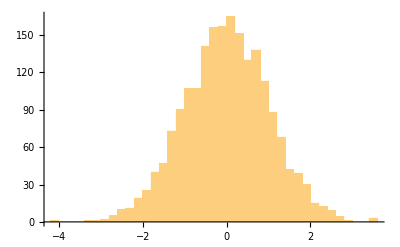

```mathematica
Histogram[results2[[3]],50]
```

```mathematica
results2[[{1,4}]]
```

{{1.01878,0.0134889},1.01909}